```mathematica
all = RandomReal[{0,1},{1000000,2}];
{insides,outsides}=GatherBy[all,√((#_⟦1⟧)^2+(#_⟦2⟧)^2)<1&];
4(Length@insides)/(Length@all)//N
```

3.14181

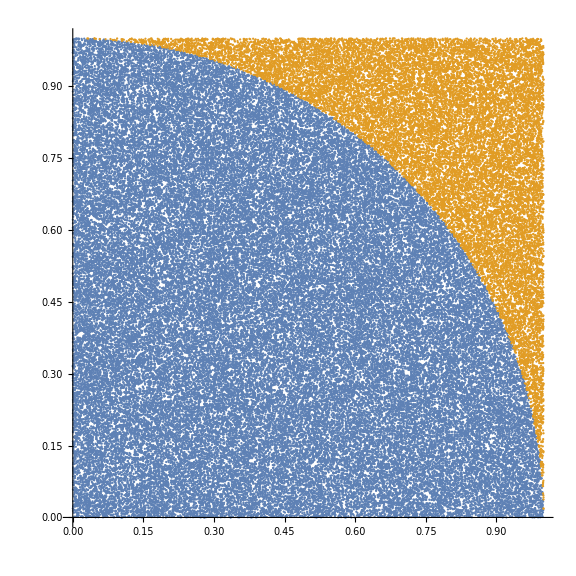

```mathematica
SetOptions[ListPlot,AspectRatio->Automatic,ImageSize->Automatic];
ListPlot@GatherBy[RandomReal[{0,1},{100000,2}],√((#_⟦1⟧)^2+(#_⟦2⟧)^2)<1&]
```

```mathematica
Manipulate[Module[{all = RandomReal[{0,1},{n,2}]},
points=GatherBy[all,√((#_⟦1⟧)^2+(#_⟦2⟧)^2)<1&];
{insides,outsides} = points;
ListPlot[points, PlotLabel->Style[4(Length@insides)/(Length@all)//N,30],AspectRatio->1,ImageSize->Large]],{n,100,100000,100},TrackedSymbols:> {n},ContinuousAction->False]
```